```mathematica
f[z_] = z^(3/2)*(2/(π z))^(1/2)Cos[ z-π/4]Exp[-z^2/(4 σ^2)];
Simplify[f[r Exp[I θ]]*Exp[-(2 π)/h r Sin[θ]], Assumptions->{r>0, h>0, σ>0}]
```

ⅇ^(-1/4 r ((ⅇ^(2 ⅈ θ) r)/σ^2+(8 π Sin[θ])/h)) √(ⅇ^(-ⅈ θ)) (ⅇ^(ⅈ θ))^(3/2) √(2/π) r Sin[π/4+ⅇ^(ⅈ θ) r]

```mathematica
Integrate[ⅇ^(-1/4 r ((ⅇ^(2 ⅈ θ) r)/σ^2+(8 π Sin[θ])/h)) ⅇ^(ⅈ θ) √(2/π) r Sin[π/4+ⅇ^(ⅈ θ) r], {θ, 0, π}, Assumptions->{h>0, σ>0, r>0}]
```

Integrate[ⅇ^(ⅈ θ-1/4 r ((ⅇ^(2 ⅈ θ) r)/σ^2+(8 π Sin[θ])/h)) √(2/π) r Sin[π/4+ⅇ^(ⅈ θ) r],{θ,0,π},Assumptions→{h>0,σ>0,r>0}]

```mathematica
Simplify[h/.Solve[x == π n(1-2 Exp[-2 π Exp[h n]]), h, Reals][[1]], Assumptions->{n>0, x>0,n π>x}]
```

Log[Log[(2 n π)/(n π-x)]/(2 π)]/n

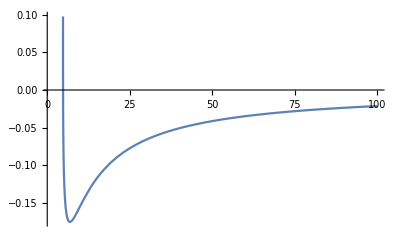

```mathematica
Plot[%258/. x-> 3*5, {n, 1, 100}]
```

```mathematica
h/.Solve[π n Tanh[π/2 Sinh[h n]] == x, h][[1]]
```

ArcSinh[(2 ArcTanh[x/(n π)])/π]/n

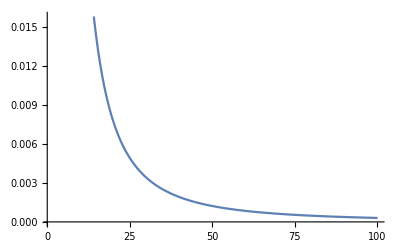

```mathematica
Plot[%263/.x-> 3*5, {n, 1, 100}]
```